```mathematica
eq=1441*a^8-254*a^7*b+196*a^6*b^2-17*a^5*b^3+7*a^4*b^4-21962*a^6*c+2958*a^5*b*c-2370*a^4*b^2*c+136*a^3*b^3*c-54*a^2*b^4*c+129440*a^4*c^2-11526*a^3*b*c^2+9244*a^2*b^2*c^2-270*a*b^3*c^2+108*b^4*c^2-339409*a^2*c^3+14928*a*b*c^3-12015*b^2*c^3+334084*c^4-13*a^4*d+a^2*b^2*d+a*b*c*d+d^2
```

1441 a^8-254 a^7 b+196 a^6 b^2-17 a^5 b^3+7 a^4 b^4-21962 a^6 c+2958 a^5 b c-2370 a^4 b^2 c+136 a^3 b^3 c-54 a^2 b^4 c+129440 a^4 c^2-11526 a^3 b c^2+9244 a^2 b^2 c^2-270 a b^3 c^2+108 b^4 c^2-339409 a^2 c^3+14928 a b c^3-12015 b^2 c^3+334084 c^4-13 a^4 d+a^2 b^2 d+a b c d+d^2

```mathematica
CoefficientList[eq/.{d->d-(-13 a^4+a^2 b^2+a b c)/2},d]//Factor
```

{1/4 (a^2-4 c) (5595 a^6-1016 a^5 b+810 a^4 b^2-68 a^3 b^3+27 a^2 b^4-65468 a^4 c+7794 a^3 b c-6240 a^2 b^2 c+270 a b^3 c-108 b^4 c+255888 a^2 c^2-14928 a b c^2+12015 b^2 c^2-334084 c^3),0,1}

```mathematica
redeq=eq/.{d->d-(-13 a^4+a^2 b^2+a b c)/2}/.{c->c+a^2/4}//Factor
```

1/16 (-15 a^6 c+8 a^5 b c-15 a^4 b^2 c+8 a^3 b^3 c+2636 a^4 c^2-5280 a^3 b c^2+3720 a^2 b^2 c^2-4320 a b^3 c^2+1728 b^4 c^2-85200 a^2 c^3+238848 a b c^3-192240 b^2 c^3+5345344 c^4+16 d^2)

```mathematica
CoefficientList[redeq,{c}]//Factor
```

{d^2,-1/16 a^3 (15 a-8 b) (a^2+b^2),1/4 (659 a^4-1320 a^3 b+930 a^2 b^2-1080 a b^3+432 b^4),-3 (1775 a^2-4976 a b+4005 b^2),334084}

```mathematica
NSolve[#==0&/@D[redeq/.{d->0},{{a,b,c}}]/.{a->1}//Factor]//DeleteDuplicates
```

{{b→-19.6016,c→7.35486},{b→1.875,c→0.},{b→1.6241,c→-0.00529004},{b→0.-1. ⅈ,c→0.},{b→0.+1. ⅈ,c→0.},{b→0.125095-0.787465 ⅈ,c→0.00290253-0.00472297 ⅈ},{b→0.125095+0.787465 ⅈ,c→0.00290253+0.00472297 ⅈ}}

```mathematica
redeq/.{d->0}//Factor
```

-1/16 c (15 a^6-8 a^5 b+15 a^4 b^2-8 a^3 b^3-2636 a^4 c+5280 a^3 b c-3720 a^2 b^2 c+4320 a b^3 c-1728 b^4 c+85200 a^2 c^2-238848 a b c^2+192240 b^2 c^2-5345344 c^3)

```mathematica
NSolve[#==0&/@D[(15 a^6-8 a^5 b+15 a^4 b^2-8 a^3 b^3-2636 a^4 c+5280 a^3 b c-3720 a^2 b^2 c+4320 a b^3 c-1728 b^4 c+85200 a^2 c^2-238848 a b c^2+192240 b^2 c^2-5345344 c^3),{{a,b,c}}]/.{a->1}//Factor]//DeleteDuplicates
```

{{b→-19.6016,c→7.35486},{b→1.6241,c→-0.00529004},{b→0.125095-0.787465 ⅈ,c→0.00290253-0.00472297 ⅈ},{b→0.125095+0.787465 ⅈ,c→0.00290253+0.00472297 ⅈ}}

```mathematica
NSolve[#==0&/@15 a^6-8 a^5 b+15 a^4 b^2-8 a^3 b^3-2636 a^4 c+5280 a^3 b c-3720 a^2 b^2 c+4320 a b^3 c-1728 b^4 c+85200 a^2 c^2-238848 a b c^2+192240 b^2 c^2-5345344 c^3)/.{a->1}//Factor]//DeleteDuplicates
```

```mathematica
NSolve[#==0&/@D[(15 a^6-8 a^5 b+15 a^4 b^2-8 a^3 b^3-2636 a^4 c+5280 a^3 b c-3720 a^2 b^2 c+4320 a b^3 c-1728 b^4 c+85200 a^2 c^2-238848 a b c^2+192240 b^2 c^2-5345344 c^3),{{a,b,c}}]/.{a->1}//Factor]//DeleteDuplicates
```

```mathematica
CoefficientList[eq/.{d->d-(-13 a^4+a^2 b^2+a b c)/2},d]//Factor
```

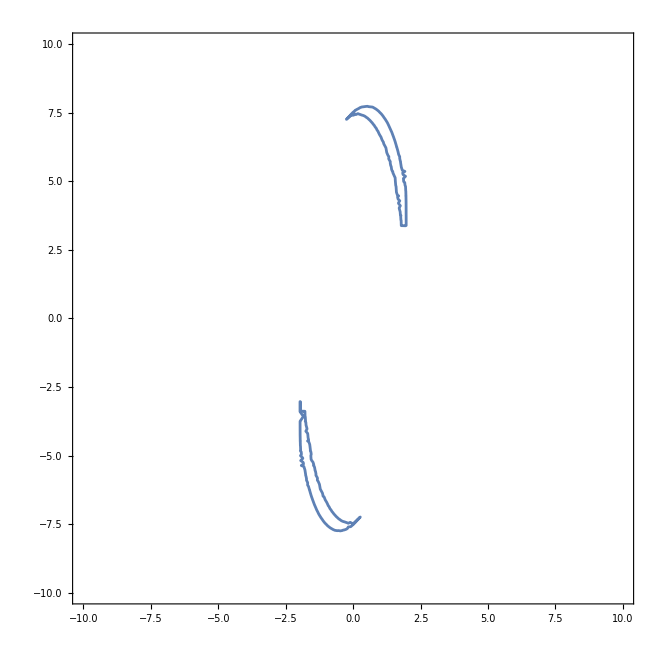

```mathematica
ContourPlot[( (a^2-4 c)(5595 a^6-1016 a^5 b+810 a^4 b^2-68 a^3 b^3+27 a^2 b^4-65468 a^4 c+7794 a^3 b c-6240 a^2 b^2 c+270 a b^3 c-108 b^4 c+255888 a^2 c^2-14928 a b c^2+12015 b^2 c^2-334084 c^3)/.{c->1})==0,{a,-10,10},{b,-10,10}]
```

```mathematica
Solve[r^2-r+1==0]
```

{{r→(-1)^(1/3)},{r→-(-1)^(2/3)}}

```mathematica
oe=(84*r+393)*a^8+(-169*r+24)*a^7*b+(4*r+64)*a^6*b^2+(-4*r-11)*a^5*b^3+7*a^4*b^4+(-955*r-6164)*a^6*c+(1919*r-155)*a^5*b*c+(-30*r-856)*a^4*b^2*c+(24*r+96)*a^3*b^3*c-54*a^2*b^4*c+(3540*r+36070)*a^4*c^2+(-7098*r-60)*a^3*b*c^2+(54*r+3690)*a^2*b^2*c^2+(-36*r-198)*a*b^3*c^2+108*b^4*c^2+(-4293*r-92400)*a^2*c^3+(8586*r+998)*a*b*c^3-5291*b^2*c^3+87808*c^4+(r-2)*a^4*d+(-2*r+2)*a^3*b*d+a^2*b^2*d+(-3*r-11)*a^2*c*d+(6*r-3)*a*b*c*d+d^2/.{r->(-1)^(1/3)}//Factor
```

393 a^8+84 (-1)^(1/3) a^8+24 a^7 b-169 (-1)^(1/3) a^7 b+64 a^6 b^2+4 (-1)^(1/3) a^6 b^2-11 a^5 b^3-4 (-1)^(1/3) a^5 b^3+7 a^4 b^4-6164 a^6 c-955 (-1)^(1/3) a^6 c-155 a^5 b c+1919 (-1)^(1/3) a^5 b c-856 a^4 b^2 c-30 (-1)^(1/3) a^4 b^2 c+96 a^3 b^3 c+24 (-1)^(1/3) a^3 b^3 c-54 a^2 b^4 c+36070 a^4 c^2+3540 (-1)^(1/3) a^4 c^2-60 a^3 b c^2-7098 (-1)^(1/3) a^3 b c^2+3690 a^2 b^2 c^2+54 (-1)^(1/3) a^2 b^2 c^2-198 a b^3 c^2-36 (-1)^(1/3) a b^3 c^2+108 b^4 c^2-92400 a^2 c^3-4293 (-1)^(1/3) a^2 c^3+998 a b c^3+8586 (-1)^(1/3) a b c^3-5291 b^2 c^3+87808 c^4-2 a^4 d+(-1)^(1/3) a^4 d+2 a^3 b d-2 (-1)^(1/3) a^3 b d+a^2 b^2 d-11 a^2 c d-3 (-1)^(1/3) a^2 c d-3 a b c d+6 (-1)^(1/3) a b c d+d^2

```mathematica
CoefficientList[oe/.{d->d-a (-2 a^3+(-1)^(1/3) a^3+2 a^2 b-2 (-1)^(1/3) a^2 b+a b^2-11 a c-3 (-1)^(1/3) a c-3 b c+6 (-1)^(1/3) b c)/2},d]//Factor
```

{1/4 (1568 a^8+340 (-1)^(1/3) a^8-(-1)^(2/3) a^8+104 a^7 b-688 (-1)^(1/3) a^7 b+4 (-1)^(2/3) a^7 b+256 a^6 b^2+22 (-1)^(1/3) a^6 b^2-4 (-1)^(2/3) a^6 b^2-48 a^5 b^3-12 (-1)^(1/3) a^5 b^3+27 a^4 b^4-24700 a^6 c-3810 (-1)^(1/3) a^6 c+6 (-1)^(2/3) a^6 c-588 a^5 b c+7674 (-1)^(1/3) a^5 b c-24 (-1)^(2/3) a^5 b c-3390 a^4 b^2 c-150 (-1)^(1/3) a^4 b^2 c+24 (-1)^(2/3) a^4 b^2 c+390 a^3 b^3 c+84 (-1)^(1/3) a^3 b^3 c-216 a^2 b^4 c+144159 a^4 c^2+14094 (-1)^(1/3) a^4 c^2-9 (-1)^(2/3) a^4 c^2-306 a^3 b c^2-28278 (-1)^(1/3) a^3 b c^2+36 (-1)^(2/3) a^3 b c^2+14751 a^2 b^2 c^2+252 (-1)^(1/3) a^2 b^2 c^2-36 (-1)^(2/3) a^2 b^2 c^2-792 a b^3 c^2-144 (-1)^(1/3) a b^3 c^2+432 b^4 c^2-369600 a^2 c^3-17172 (-1)^(1/3) a^2 c^3+3992 a b c^3+34344 (-1)^(1/3) a b c^3-21164 b^2 c^3+351232 c^4),0,1}

```mathematica
(1568 a^8+340 (-1)^(1/3) a^8-(-1)^(2/3) a^8+104 a^7 b-688 (-1)^(1/3) a^7 b+4 (-1)^(2/3) a^7 b+256 a^6 b^2+22 (-1)^(1/3) a^6 b^2-4 (-1)^(2/3) a^6 b^2-48 a^5 b^3-12 (-1)^(1/3) a^5 b^3+27 a^4 b^4-24700 a^6 c-3810 (-1)^(1/3) a^6 c+6 (-1)^(2/3) a^6 c-588 a^5 b c+7674 (-1)^(1/3) a^5 b c-24 (-1)^(2/3) a^5 b c-3390 a^4 b^2 c-150 (-1)^(1/3) a^4 b^2 c+24 (-1)^(2/3) a^4 b^2 c+390 a^3 b^3 c+84 (-1)^(1/3) a^3 b^3 c-216 a^2 b^4 c+144159 a^4 c^2+14094 (-1)^(1/3) a^4 c^2-9 (-1)^(2/3) a^4 c^2-306 a^3 b c^2-28278 (-1)^(1/3) a^3 b c^2+36 (-1)^(2/3) a^3 b c^2+14751 a^2 b^2 c^2+252 (-1)^(1/3) a^2 b^2 c^2-36 (-1)^(2/3) a^2 b^2 c^2-792 a b^3 c^2-144 (-1)^(1/3) a b^3 c^2+432 b^4 c^2-369600 a^2 c^3-17172 (-1)^(1/3) a^2 c^3+3992 a b c^3+34344 (-1)^(1/3) a b c^3-21164 b^2 c^3+351232 c^4)//Factor
```

1568 a^8+340 (-1)^(1/3) a^8-(-1)^(2/3) a^8+104 a^7 b-688 (-1)^(1/3) a^7 b+4 (-1)^(2/3) a^7 b+256 a^6 b^2+22 (-1)^(1/3) a^6 b^2-4 (-1)^(2/3) a^6 b^2-48 a^5 b^3-12 (-1)^(1/3) a^5 b^3+27 a^4 b^4-24700 a^6 c-3810 (-1)^(1/3) a^6 c+6 (-1)^(2/3) a^6 c-588 a^5 b c+7674 (-1)^(1/3) a^5 b c-24 (-1)^(2/3) a^5 b c-3390 a^4 b^2 c-150 (-1)^(1/3) a^4 b^2 c+24 (-1)^(2/3) a^4 b^2 c+390 a^3 b^3 c+84 (-1)^(1/3) a^3 b^3 c-216 a^2 b^4 c+144159 a^4 c^2+14094 (-1)^(1/3) a^4 c^2-9 (-1)^(2/3) a^4 c^2-306 a^3 b c^2-28278 (-1)^(1/3) a^3 b c^2+36 (-1)^(2/3) a^3 b c^2+14751 a^2 b^2 c^2+252 (-1)^(1/3) a^2 b^2 c^2-36 (-1)^(2/3) a^2 b^2 c^2-792 a b^3 c^2-144 (-1)^(1/3) a b^3 c^2+432 b^4 c^2-369600 a^2 c^3-17172 (-1)^(1/3) a^2 c^3+3992 a b c^3+34344 (-1)^(1/3) a b c^3-21164 b^2 c^3+351232 c^4

```mathematica
Solve[t a-s b==0,a]
```

{{a→(b s)/t}}

```mathematica
redeq/.{a->(b s)/t}//Factor
```

-1/(16 t^6)(15 b^6 c s^6-8 b^6 c s^5 t+15 b^6 c s^4 t^2-2636 b^4 c^2 s^4 t^2-8 b^6 c s^3 t^3+5280 b^4 c^2 s^3 t^3-3720 b^4 c^2 s^2 t^4+85200 b^2 c^3 s^2 t^4+4320 b^4 c^2 s t^5-238848 b^2 c^3 s t^5-1728 b^4 c^2 t^6+192240 b^2 c^3 t^6-5345344 c^4 t^6-16 d^2 t^6)

```mathematica
y^2-x(x-1)(x-l)/.{x->1/x,y->y/x^(2)}//Factor//Numerator
```

-x+x^2+l x^2-l x^3+y^2

```mathematica
-x+x^2+l x^2-l x^3//Factor
```

-((-1+x) x (-1+l x))

```mathematica
x/.{x->1/x}/.{x->1-x}//Factor
```

-1/(-1+x)

```mathematica
x/.{x->1/(1-x)}/.{x->1/(1-x)}//Factor
```

(-1+x)/x

```mathematica
(-1+Sqrt[5])/2
```

1/2 (-1+√5)

```mathematica
N[1/2 (-1+√5)]
```

0.618034

```mathematica
-(-c1+c1 c2)/((-1+c1) c2)//Factor
```

-(c1 (-1+c2))/((-1+c1) c2)

```mathematica
Y^2-X(X-1)(X-c1)/.{X->s^2(-(-c1+c1 c2)/((-1+c1) c2)+x^2),Y->s^3y}/.{y->0}/.{s->((c1-1)c2/(c1-c2))^(1/2)}//Factor
```

((-1+c1)^2 c2 (-1+x) (1+x) (c1-c2 x^2) (c1-c1 c2-c2 x^2+c1 c2 x^2))/(c1-c2)^3

```mathematica
Solve[(-1+x) (1+x) (c1-c2 x^2) (c1-c1 c2-c2 x^2+c1 c2 x^2)==0,x]
```

{{x→-1},{x→1},{x→-(√c1)/(√c2)},{x→(√c1)/(√c2)},{x→-(√c1 √(-1+c2))/(√(-c2+c1 c2))},{x→(√c1 √(-1+c2))/(√(-c2+c1 c2))}}

```mathematica
(1-c1)X/(X-c1)/.{X->s^2(-(-c1+c1 c2)/((-1+c1) c2)+x^2),Y->s^3y}/.{s->((c1-1)c2/(c1-c2))^(1/2)}//Factor
```

(c1-c1 c2-c2 x^2+c1 c2 x^2)/(c1-c2 x^2)

```mathematica
(c1-c1 c2-c2 x^2+c1 c2 x^2)/(c1-c2+c1 c2-c1^2 c2-c1 c2 x^2+c1^2 c2 x^2)/.{x->-(√c1 √(-1+c2))/(√(-c2+c1 c2))}//Factor
```

0

```mathematica
Y^2-X(X-1)(X-c1)/.{X->s^2(-(-c1+c1 c2)/((-1+c1) c2)+x^2),Y->s^3y}/.{s->((c1-1)c2/(c1-c2))^(1/2)}//Factor
```

((-1+c1)^2 c2 (-c1^2+c1^2 c2+c1^2 x^2+2 c1 c2 x^2-2 c1^2 c2 x^2-c1 c2^2 x^2-2 c1 c2 x^4+c1^2 c2 x^4-c2^2 x^4+2 c1 c2^2 x^4+c2^2 x^6-c1 c2^2 x^6-c2^2 y^2+c1 c2^2 y^2))/(c1-c2)^3

```mathematica
x^6(Y^2-X(X-1)(X-c2))/.{X->-s^2((-c2+c1 c2)/(c1 (-1+c2))-1/x^2),Y->s^3y/x^3}/.{y->0}/.{s->((c2-1)c1/(c2-c1))^(1/2)}//Factor
```

(c1 (-1+c2)^2 (-1+x) (1+x) (c1-c2 x^2) (c1-c1 c2-c2 x^2+c1 c2 x^2))/(c1-c2)^3

```mathematica
(1-c2)X/(X-c2)/.{X->-s^2((-c2+c1 c2)/(c1 (-1+c2))-1/x^2),Y->s^3y/x^3}/.{y->0}/.{s->((c2-1)c1/(c2-c1))^(1/2)}//Factor
```

(c1-c1 c2-c2 x^2+c1 c2 x^2)/(c1-c2 x^2)

```mathematica
(c1-c1 c2-c2 x^2+c1 c2 x^2)/(c1-c2 x^2)/.{x->1}
```

1

```mathematica
(c1-c1 c2-c2 x^2+c1 c2 x^2)/c2//Expand
```

-c1+c1/c2-x^2+c1 x^2

```mathematica
\f
```

```mathematica
Simplify[(c1-c1 c2-c2 x^2+c1 c2 x^2)/c2]
```

-x^2+c1 (-1+1/c2+x^2)

```mathematica
(c1-c1 c2-c2 x^2+c1 c2 x^2)/(c1 c2-c1 c2^2+c1 x^2-c2 x^2-c1 c2 x^2+c1 c2^2 x^2)
```

c2/(1-c2+c2^2)

```mathematica
c1 c2-c1 c2^2+c1 x^2-c2 x^2-c1 c2 x^2+c1 c2^2 x^2==0
```

c1 c2-c1 c2^2+c1 x^2-c2 x^2-c1 c2 x^2+c1 c2^2 x^2==0

```mathematica
Solve[c1 c2-c1 c2^2+c1 x^2-c2 x^2-c1 c2 x^2+c1 c2^2 x^2==0,{x},Reals]
```

{{x→ConditionalExpression[-√((-c1 c2+c1 c2^2)/(c1-c2-c1 c2+c1 c2^2)), ]},{x→ConditionalExpression[√((-c1 c2+c1 c2^2)/(c1-c2-c1 c2+c1 c2^2)), ]}}

```mathematica
x^6(Y^2-X(X-1)(X-c2))/.{X->s^2((-c2+c1 c2)/(c1 (-1+c2))-1/x^2),Y->s^3y/x^3}/.{s->((c2-1)c1/(c1-c2))^(1/2)}//Factor
```

-(c1 (-1+c2)^2 (c1^2-c1^2 c2-c1^2 x^2-2 c1 c2 x^2+2 c1^2 c2 x^2+c1 c2^2 x^2+2 c1 c2 x^4-c1^2 c2 x^4+c2^2 x^4-2 c1 c2^2 x^4-c2^2 x^6+c1 c2^2 x^6+c1^2 y^2-c1^2 c2 y^2))/(c1-c2)^3

```mathematica
Solve[((-c1+c1 c2-c2 x^2+c1 c2 x^2) (-c1 s^2+c1 c2 s^2+c1 x^2-c1 c2 x^2-c2 s^2 x^2+c1 c2 s^2 x^2) (-c1 s^2+c1 c2 s^2+c1 c2 x^2-c1 c2^2 x^2-c2 s^2 x^2+c1 c2 s^2 x^2))/((-1+c1)^3 c2^3)==0,x]
```

{{x→-(√(c1-c1 c2))/(√(-c2+c1 c2))},{x→(√(c1-c1 c2))/(√(-c2+c1 c2))},{x→-(√(c1 s^2-c1 c2 s^2))/(√(c1-c1 c2-c2 s^2+c1 c2 s^2))},{x→(√(c1 s^2-c1 c2 s^2))/(√(c1-c1 c2-c2 s^2+c1 c2 s^2))},{x→-(ⅈ √c1 √(-1+c2) s)/(√(c1 c2-c1 c2^2-c2 s^2+c1 c2 s^2))},{x→(ⅈ √c1 √(-1+c2) s)/(√(c1 c2-c1 c2^2-c2 s^2+c1 c2 s^2))}}

```mathematica
Solve[(√(c1 s^2-c1 c2 s^2))/(√(c1-c1 c2-c2 s^2+c1 c2 s^2))==1,s]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s→-(√c1 √(-1+c2))/(√(-c1-c2+2 c1 c2))},{s→(√c1 √(-1+c2))/(√(-c1-c2+2 c1 c2))}}

```mathematica
CoefficientList[x^3+(-c1^2-2*c1*c2+2*c1+c2)/(c1*c2-c2)*x^2*z-y^2*z+(2*c1^2*c2+c1*c2^2-c1^2-2*c1*c2)/(c1*c2^2-c2^2)*x*z^2+(-c1^2*c2+c1^2)/(c1*c2^2-c2^2)*z^3/.{x->x+(-c1+c1 c2)/((-1+c1) c2)z}/.{x->s^2 x,y->s^3 y}/.{s->((c1-c2)/((-1+c1) c2))^(1/2)},{y,x}]//Factor
```

{{0,(c1 (c1-c2)^3)/((-1+c1)^3 c2^3),-((1+c1) (c1-c2)^3)/((-1+c1)^3 c2^3),(c1-c2)^3/((-1+c1)^3 c2^3)},{0,0,0,0},{-(c1-c2)^3/((-1+c1)^3 c2^3),0,0,0}}

```mathematica
{x^2*z-((-c1+c1*c2)*z^3)/((-1+c1)*c2),y,z^3}/.{z->1}
```

{-(-c1+c1 c2)/((-1+c1) c2)+x^2,y,1}

```mathematica
{x^2*z+(-c1+c1 c2)/((-1+c1) c2)z^3,y,z^3}//InputForm
```

{x^2*z + ((-c1 + c1*c2)*z^3)/((-1 + c1)*c2), y, z^3}

```mathematica
CoefficientList[x^3+(-c1^2-2*c1*c2+2*c1+c2)/(c1*c2-c2)*x^2*z-y^2*z+(2*c1^2*c2+c1*c2^2-c1^2-2*c1*c2)/(c1*c2^2-c2^2)*x*z^2+(-c1^2*c2+c1^2)/(c1*c2^2-c2^2)*z^3/.{z->1}/.{x->x+(-c1+c1 c2)/((-1+c1) c2)},{y,x}]//Factor
```

{{0,(c1 (c1-c2)^2)/((-1+c1)^2 c2^2),-((1+c1) (c1-c2))/((-1+c1) c2),1},{0,0,0,0},{-1,0,0,0}}

```mathematica
x^3+(-c1^2-2*c1*c2+2*c1+c2)/(c1*c2-c2)*x^2*z-y^2*z+(2*c1^2*c2+c1*c2^2-c1^2-2*c1*c2)/(c1*c2^2-c2^2)*x*z^2+(-c1^2*c2+c1^2)/(c1*c2^2-c2^2)*z^3/.{x->x+(-c1+c1 c2)/((-1+c1) c2)z,y->0}//Factor
```

-(x (-c2 x+c1 c2 x-c1 z+c2 z) (c2 x-c1 c2 x+c1^2 z-c1 c2 z))/((-1+c1)^2 c2^2)

```mathematica
{x,y,z}/.{x->x+(-c1+c1 c2)/((-1+c1) c2)z}/.{x->s^2 x,y->s^3 y}/.{s->((c1-c2)/((-1+c1) c2))^(1/2)}//Factor
```

{(c1 x-c2 x-c1 z+c1 c2 z)/((-1+c1) c2),((c1-c2)/((-1+c1) c2))^(3/2) y,z}

```mathematica
Solve[(c1-c1 c2-c2 s+c1 c2 s)==0,s]
```

{{s→(-c1+c1 c2)/((-1+c1) c2)}}

```mathematica
CoefficientList[-y^2+x(x-1)(x-c1),{y,x}]
```

{{0,c1,-1-c1,1},{0,0,0,0},{-1,0,0,0}}

```mathematica
CoefficientList[x^3+(-2*c1*c2-c2^2+c1+2*c2)/(c1*c2-c1)*x^2*z+(c1*c2^2-c2^2)/(c1^2*c2-c1^2)*y^2*z+(c1^2*c2+2*c1*c2^2-2*c1*c2-c2^2)/(c1^2*c2-c1^2)*x*z^2+(-c1*c2^2+c2^2)/(c1^2*c2-c1^2)*z^3/.{z->1,x->x+(-c2+c1 c2)/(c1 (-1+c2))},{y,x}]//Factor
```

{{0,((c1-c2)^2 c2)/(c1^2 (-1+c2)^2),((c1-c2) (1+c2))/(c1 (-1+c2)),1},{0,0,0,0},{((-1+c1) c2^2)/(c1^2 (-1+c2)),0,0,0}}

```mathematica
Solve[((-1+s) (-c2+c1 s) (c2-c1 c2-c1 s+c1 c2 s))/(c1^2 (-1+c2))==0,s]
```

{{s→1},{s→c2/c1},{s→(-c2+c1 c2)/(c1 (-1+c2))}}

```mathematica
x/(s x+(1-s))/.{s->1/(1-c)}//Factor
```

-((-1+c) x)/(-c+x)